```mathematica
dir="D:\\better output 2";
GetParent[orgNo_]:=Module[{path,g,n,i},
Quiet[
path = StringForm["``\\organisms\\org``.json",dir,orgNo];
{g,n,i}=Import[path//ToString];
"parent"/.i
]
]
GetLivingOrganisms[frameNo_]:=Module[{path,i,items,organisms},
path = StringForm["``\\output\\frame``.json",dir,frameNo];
{i}=Import[path//ToString];
items = "Items"/.i;
organisms="o"/.items//DeleteDuplicates;
Select[organisms,#>=0&]
]
```

```mathematica
NestWhileList[GetParent,2,#≥0&]
```

{2,0,-1}

```mathematica
step = 16346000;
currGenomeIndex = 76903;
```

```mathematica
edges =ParallelMap[GetParent[#]->#&,Table[o,{o,0,currGenomeIndex}]];
living = GetLivingOrganisms[step];
```

```mathematica
g=Graph[edges];
Graph[edges,GraphHighlight->living∩VertexList[g],VertexLabels->Placed["Name",Tooltip]]
```

-Graphics-

-Graphics-

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
parents=ParallelMap[GetParent,Table[o,{o,0,currGenomeIndex}]];
nParents=Transpose[Tally[parents]][[2]];
nInfertile=currGenomeIndex-Total[nParents];
nOneChild=Count[nParents,1];
nTwoChildren=Count[nParents,2];
nMoreThanTwo=Count[nParents,u_/;u> 2];
val={nInfertile,nOneChild,nTwoChildren,nMoreThanTwo};
```

$Aborted

Tally::list: List expected at position 1 in Tally[parents].

Part::partw: Part 2 of Transpose[Tally[parents]] does not exist.

```mathematica
pie=PieChart[val,ChartLegends->{
"No children",
"One child",
"Two children",
 ">2 children"},
PlotLabel->"Proportion of different number of offsprings",
ChartLabels->Placed[StringForm["``%",N[(100#)/Total[val],3]]&/@val,"RadialOutside"],
ChartLabels->"%",ImageSize->Medium]
```

-Graphics-

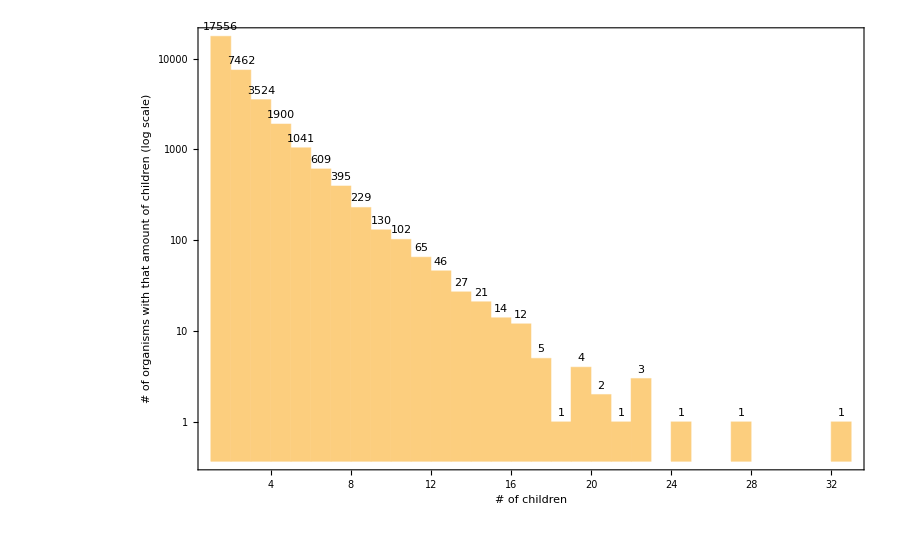

```mathematica
plot=Histogram[nParents, ScalingFunctions->{"Linear","Log"},LabelingFunction->Above,PlotRange->All,ImageSize->900,
Frame->{{True,False},{True,False}},
FrameLabel->{"# of children","# of organisms with that amount of children (log scale)"}]
```

```mathematica
Max[nParents]
```

2520

```mathematica
Mean[nParents]//N
```

1260.5

```mathematica
Export["C:\\Users\\admin\\Documents\\Joakim\\children histogram.png",plot,"PNG",ImageResolution->300]
```

C:\Users\admin\Documents\Joakim\children histogram.png

```mathematica
Export["C:\\Users\\admin\\Documents\\Joakim\\children pie.png",pie,"PNG",ImageResolution->300]
```

C:\Users\admin\Documents\Joakim\children pie.png

```mathematica
Median[nParents]//N
```

1.